```mathematica
Integrate[x*(1+x)^(-4),{x,0,Infinity}]
```

1/6

```mathematica
Integrate[c*x,{x,0,1}]
```

c/2

```mathematica
Integrate[2*x^2,{x,0,1}]
```

2/3

```mathematica
Integrate[2*x^3,{x,0,1}]
```

1/2

```mathematica
Out[4]-(Out[3])^2
```

1/18

```mathematica
N[Sqrt[%]]
```

0.235702

```mathematica
N[%/Out[3]]
```

0.353553

```mathematica
Integrate[x/7,{x,1,8}]
```

9/2

```mathematica
Integrate[x^2/7,{x,1,8}]
```

73/3

```mathematica
Sqrt[%-4.5^2]
```

2.02073

```mathematica
Integrate[Sqrt[x+1]/7,{x,1,8}]
```

18/7-(4 √2)/21

```mathematica
N[%]
```

2.30205

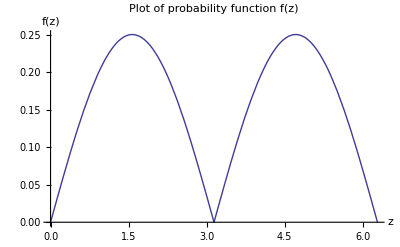

```mathematica
Plot[Abs[Sin[z]]/4,{z,0,2*Pi},AxesLabel-> {"z","f(z)"},PlotLabel -> "Plot of probability function f(z)"]
```

```mathematica
Integrate[z*Abs[Sin[z]]/4,{z,0,2*Pi}]
```

π

```mathematica
Integrate[Abs[Sin[x]]/4,{x,0,Pi}]
```

1/2

```mathematica
Integrate[Sin[z]/4,z]
```

-Cos[z]/4

```mathematica
D[Abs[Sin[z]]/4,{z,1}]
```

1/4 Cos[z] Abs'[Sin[z]]

```mathematica
Solve[1/4 Cos[z] Abs'[Sin[z]]==0,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→-π/2},{z→π/2},{z→ArcSin[InverseFunction[Abs',1,1][0]]}}

```mathematica
F[x_]:=(1/9)*(2x^2-x^3/3)
```

```mathematica
F[x]
```

1/9 (2 x^2-x^3/3)

```mathematica
D[F[x],{x,1}]
```

1/9 (4 x-x^2)

```mathematica
D[%,{x,1}]
```

1/9 (4-2 x)

```mathematica
Solve[1/9 (4-2 x)==0,x]
```

{{x→2}}

```mathematica
x=2
```

2

```mathematica
1/9 (4 x-x^2)
```

4/9